```mathematica
Задание 1. инерполяция по Лагранжу(11 вариант);
lgr[ta_,n_,x_]:=∑_(i=1)^n ta[[i,2]]*(∏_(j=1)^n If[j≠i,(x-ta[[j,1]])/(ta[[i,1]]-ta[[j,1]]),1]);
```

```mathematica
TA = {{0.4,0.5},{0.6,1.375},{0.8,1.5},{1,1.75},{1.2,1.625}}; TableForm[TA]
```

0.4 | 0.5
0.6 | 1.375
0.8 | 1.5
1 | 1.75
1.2 | 1.625

```mathematica
y[x_]:=lgr[TA,Length[TA],x]
y[z]
```

13.0208 (-1.2+z) (-1+z) (-0.8+z) (-0.6+z)-143.229 (-1.2+z) (-1+z) (-0.8+z) (-0.4+z)+234.375 (-1.2+z) (-1+z) (-0.6+z) (-0.4+z)-182.292 (-1.2+z) (-0.8+z) (-0.6+z) (-0.4+z)+42.3177 (-1+z) (-0.8+z) (-0.6+z) (-0.4+z)

```mathematica
y1[z_]:=Expand[y[z]]
y1[z]
```

-13.875+76.8229 z-143.88 z^2+118.49 z^3-35.8073 z^4

```mathematica
Задание 2. Проверка решения по заданию 1;
```

```mathematica
yp[z_]:=InterpolatingPolynomial[TA,z];Expand[yp[z]]
```

-13.875+76.8229 z-143.88 z^2+118.49 z^3-35.8073 z^4

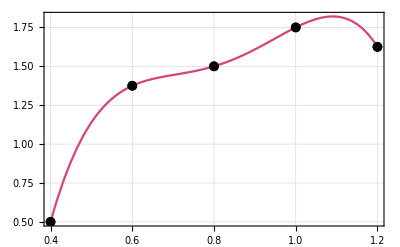

```mathematica
Задание 3. Построить графики;
ploty:=Plot[y[z],{z,0.4,1.2},Frame->True,GridLines->Automatic,ColorFunction->Function[{x,y},Hue[x]]]
listplot:=ListPlot[TA,Mesh->Full,PlotStyle->Black,PlotMarkers->{Automatic, Medium}]
Show[ploty,listplot]
```

```mathematica
Задание 4. Погрешность интерполяции аналитически заданной функции;
```

```mathematica
f[x_]:=√x-2*Cos[x];
fn[x_,n_]:=Dt[f[x],{x,n}];
f5[x_]=N[fn[x,5]];f5[x]
```

3.28125/x^(9/2)+2. Sin[x]

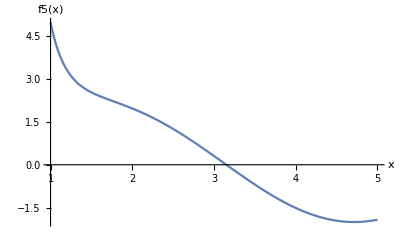

```mathematica
Plot[f5[x],{x,1,5},AxesLabel->{"x","f5(x)"}]
```

```mathematica
m=Abs[f5[1]]
```

4.96419

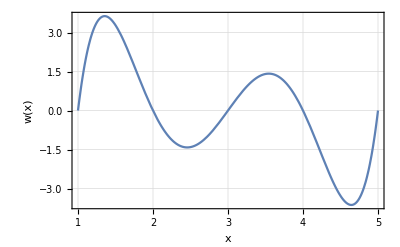

```mathematica
Om[Ta_,n_,x_]:=∏_(i=1)^n (x-Ta[[i]]);
Ta={1,2,3,4,5};
Plot[Om[Ta,Length[Ta],x],{x,1,5},Frame->True,GridLines->Automatic,FrameLabel->{"x","w(x)"}]
```

```mathematica
mf = FindMinimum[Om[Ta,Length[Ta],x],{x,4}]
```

{-3.63143,{x→4.64443}}

```mathematica
ri=m*Abs[mf[[1]]]/5!
```

0.150226

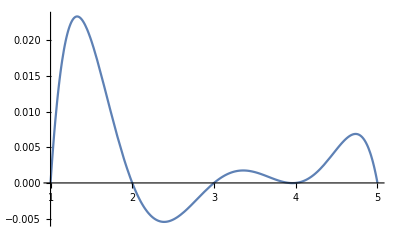

```mathematica
f1=Table[{Ta[[i]],f[Ta[[i]]]},{i,1,5}];
Ipol=InterpolatingPolynomial[f1,x];
r=f[x]-Ipol;
Plot[r,{x,1,5}]
```

```mathematica
rmax = FindMaximum[r,{x,2}]
```

{0.0233712,{x→1.32546}}

```mathematica
Задание 5. Рациональный выбор узлов
```

```mathematica
a=1;b=5;
n=Length[Ta]-1;
Do[y[i]=-Cos[(2*(i-1)+1)/(2*n+2)*π];
	Uzel[i]=N[(b+a)/2+(b-a)/2*y[i]];
Ta2=Table[Uzel[i],{i,n+1}],{i,1,n+1}]
TableForm[Ta2]
```

1.09789
1.82443
3.
4.17557
4.90211

```mathematica
Plot[Om[Ta,Length[Ta2],x],{x,1,5},Frame->True,GridLines->Automatic,FrameLabel->{"x","w(x)"}]
```

-Graphics-

```mathematica
mf2 = FindMinimum[Om[Ta2,Length[Ta2],x],{x,4}]
```

{-2.,{x→4.61803}}

```mathematica
ri2=m*Abs[mf2[[1]]]/5!
```

0.0827365

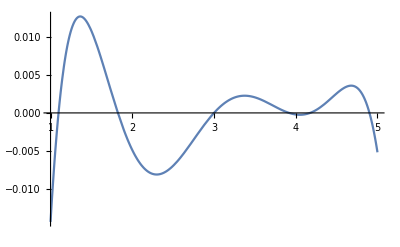

```mathematica
f2=Table[{Ta2[[i]],f[Ta2[[i]]]},{i,1,5}];
Ipol2=InterpolatingPolynomial[f2,x];
r2=f[x]-Ipol2;
Plot[r2,{x,1,5}]
```

```mathematica
rmax2 = FindMaximum[r2,{x,1}]
```

{0.0127135,{x→1.36316}}